# Little Tests, One pyramidal lvl

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],"1DPackage","*"}]
$Path=Join[$Path,FileNames[packageDirectory]];
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\1DPackage\*

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedNewMethod"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseAEREAL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Aereal",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
reduce=2;
path1=FileNameJoin[{baseAEREAL,"Aereal1.png"}];
path2=FileNameJoin[{baseAEREAL,"Aereal2.png"}];
pathResult=FileNameJoin[{baseAEREAL,"AerealResult.png"}];

rgb2d[{r_,g_,b_}]:=r*4+g/64;
clean[img_]:=Image[ImageData[img]];

reduire[img_,1]:=img;
reduire[img_,factor_]:=ImageResize[img,ImageDimensions[img]/factor];

iaa=reduire[ColorConvert[clean@Import[path1],"GrayScale"],reduce];
ibb=reduire[ColorConvert[clean@Import[path2],"GrayScale"],reduce];
iccolor=reduire[clean@Import[pathResult],reduce];

Show[iaa]
```

-Graphics-

## Image sections

```mathematica
(*{1,44},{1,102} arbitrary size to make the method faster *)
listDims={{500,500}}
ims=Table[
nx=dims[[1]]/reduce;
ny=dims[[2]]/reduce;


{ia,ib,icolor}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{iaa,ibb,iccolor};
{ia,ib}
,{dims,listDims}]
```

{{500,500}}

{{-Graphics-,-Graphics-}}

## V0 function

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

## Little functions

```mathematica
bigTest[steps_,dis_,n_,u_,listv0_,condition_,e_,minmaxList_,imslist_]:=Block[{ic,depth, resTable,realPVTable,okTable,realOkPVTable,pos,pv,g0,nonresTable,nonrealPVTable},(
Table[
Table[
ic=move[im[[1]],dis];
depth=stereoDepth[n,u,listv0,condition,im[[1]],ic,minmax[[2]],minmax,Range[1,103,steps],Range[1,45],e,"ConstrainedNewMethod"];

(* We only keep converged solutions *)
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,resTable[[r,All,1]]}]
,{r,45}];

(* We only keep ok solutions *)
okTable=Table[
Select[depth[[r]],#[[2]]=="ok"&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
realOkPVTable=Table[
pos=okTable[[r,All,5]]-okTable[[r,All,3]];
pv=Thread[{pos,okTable[[r,All,1]]}]
,{r,45}];

(* We only keep NON converged solutions *)
nonresTable=Table[
Select[depth[[r]],(#[[2]]!="converged"&&#[[2]]!="ok")&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
nonrealPVTable=Table[
pos=nonresTable[[r,All,5]]-nonresTable[[r,All,3]];
pv=Thread[{pos,nonresTable[[r,All,1]]}]
,{r,45}];

(* We create g0 *)
g0=Graphics[{PointSize[0.009],Table[affiche[#,45-y]&/@realPVTable[[y]],{y,1,45}]}];
g0=Rasterize[Show[im[[1]],g0],ImageSize->ImageDimensions[im[[1]]]*5,ImageResolution->300];

{realPVTable,realOkPVTable,nonrealPVTable,g0}

,{minmax,minmaxList}]
,{im, imslist}]
)]
```

## Big Tests

### Test Design

For a synthetical displacement of 0.1:
 
•	Initial values range: {{0,1},{-1,1},{-1,0},{-2,2}}
•	Selection criteria:
	•	We filter direction (positive solutions only)
	•	Range {0, 1} 
	•	No errors allowed
•	Magnitude threshold for gradient is e=0.0001

(* Criterias to select a solution *)

newValCon=Select[tableNewVals,(#[[3]]==”converged”&& #[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
newValAny=Select[tableNewVals,((#[[3]]≠ “ok”||#[[3]]≠ “oksign”||#[[3]]≠ “okmag”||#[[3]]≠ “converged”)&&#[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
newValOk=Select[tableNewVals,((#[[3]]==”ok”||#[[3]]==”oksign”||#[[3]]==”okmag”)&& #[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
noFakeConverge=Select[tableNewVals,(#[[3]]≠ “ok”||#[[3]]≠ “oksign”||#[[3]]≠ “okmag”||#[[3]]≠ “converged”)&,1];

### Test Run

```mathematica
(* Test values *)
testLevels={{1,1}};
disList={-2,-1,-0.1,0.1,1,2};
e=0.0001;
n=0;
u=0;
steps=1;
```

```mathematica
(* Creating initial values *)
range={-3,3};
r=Random[];
listv0=Select[RandomReal[range,{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-50];
```

```mathematica
(* Creating condition *)
topbot={-3,3};
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && topbot[[1]]<Total[x[[1;;2]]]<topbot[[2]];
```

```mathematica
(* Scaling results *)
scale=topbot;
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,scale,{0,1}]],Point[{p-0.5,y+0.5}]};
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
```

```mathematica
levelTable=Table[Table[

bigTest[steps,dis,n,u,listv0,condition,e,{levels},ims]

,{levels,testLevels}],{dis,disList}];
```

```mathematica
(*selectrion criteria, level, image, extra, kind of result, rows *)
Dimensions[levelTable]
```

{6,1,1,1,4}

### Histogram Grid 1

```mathematica
fontsize=20;
imagesize=500;
maxvalue={{-3,3},{0,1000}};
bar=50;
```

```mathematica
histogramGrid=Table[
Table[

convergedData=Flatten[levelTable[[which,idxims,1,1,1,All,All,2]]];
okData=Flatten[levelTable[[which,idxims,1,1,2,All,All,2]]];
nonConvergedData=Flatten[levelTable[[which,idxims,1,1,3,All,All,2]]];

std=StandardDeviation[convergedData];
mu=Mean[convergedData];
density=(Length[Flatten[DeleteDuplicates[#]&/@Round[levelTable[[which,idxims,1,1,1,All,All,1]]]]])/(103.*45.);
meanError=Mean[Abs[0.1-convergedData]];

Histogram[{convergedData, nonConvergedData,okData},bar,
PlotLabel->Column[{
Style[Row[{"Distance= ",disList[[which]]}],FontSize->fontsize,FontFamily->"Times",Italic],
Style[Row[{"Standard deviation= ",NumberForm[std,3]}],FontSize->fontsize,FontFamily->"Times",Italic],
Style[Row[{"Mean= ",NumberForm[mu,3]}],FontSize->fontsize, FontFamily->"Times",Italic],
Style[Row[{"Mean error= ",NumberForm[meanError,2]}],FontSize->fontsize, FontFamily->"Times",Italic],
Style[Row[{"Density= ",NumberForm[density,3]}],FontSize->fontsize, FontFamily->"Times",Italic]},
Spacings->0.1,
Alignment->Center],
PlotRange->maxvalue,
ImageSize->imagesize,
AxesLabel->{Style["v",FontSize->fontsize,FontFamily->"Times",Italic],Style["n",FontSize->fontsize,FontFamily->"Times",Italic]},ChartStyle->{LightOrange,LightBlue,LightGreen}]
,{which,(*{1,4,5}*)Length[disList]}],{idxims,Length[ims]}];
```

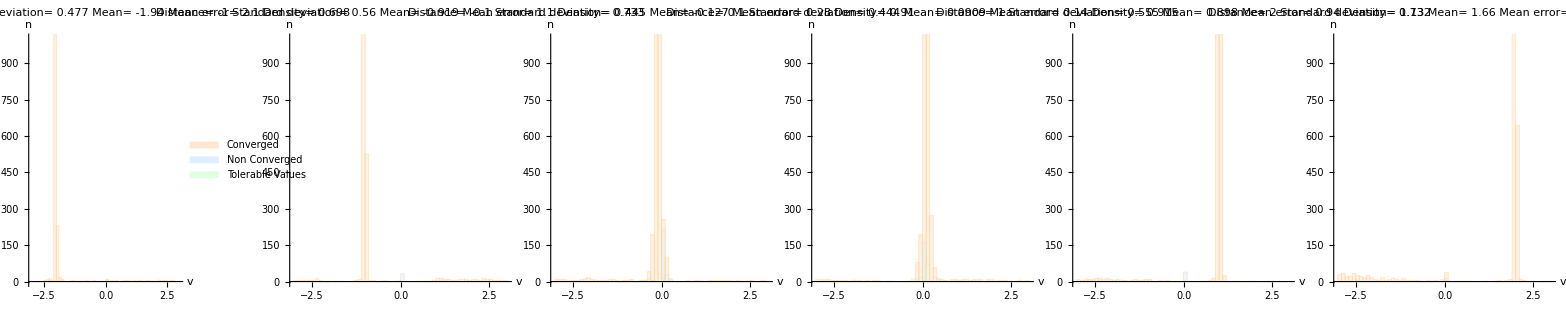

```mathematica
hFinal=Legended[
Grid[histogramGrid],
Placed[SwatchLegend[{LightOrange, LightBlue, LightGreen},{"Converged", "Non Converged", "Tolerable Values"},LegendLayout->"Row"],Below]]
```

```mathematica
nbname=StringDelete[Last@FileNameSplit@NotebookFileName[],".nb"];
```

```mathematica
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"figs"}];

Export[FileNameJoin[{figsDirectory,nbname<>"-hist.pdf"}],hFinal]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\synaereal-range-hist.pdf

### Images

```mathematica
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}]];
```

```mathematica
imagesTable=Table[

Grid[{{levelTable[[which,1,1,1,4]]},{Style[Style[Row[{"Distance= ",disList[[which]]}],FontSize->fontsize,FontFamily->"Times",Italic],FontSize->fontsize,FontFamily->"Times",Italic]}}]

,{which,(*{1,4,5}*)Length[disList]}];

imFinal=Legended[Grid[Partition[imagesTable,3]],legendBar]
```

-Graphics-
Distance= -2 | -Graphics-
Distance= -1 | -Graphics-
Distance= -0.1
-Graphics-
Distance= 0.1 | -Graphics-
Distance= 1 | -Graphics-
Distance= 2

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-im.pdf"}],imFinal]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\synaereal-range-im.pdf

### Table

```mathematica
tableValues=Table[
Table[

convergedData=Flatten[levelTable[[which,idxims,1,1,1,All,All,2]]];

std=StandardDeviation[convergedData];
mu=Mean[convergedData];
density=(Length[Flatten[DeleteDuplicates[#]&/@Round[levelTable[[which,idxims,1,1,1,All,All,1]]]]])/(103.*45.);
meanError=Mean[Abs[0.1-convergedData]];

{std,mu,density,meanError}

,{idxims,Length[ims]}],{which,Length[disList]}];
```

```mathematica
makeTable=Table[
values=tableValues[[All,All,which]];
greenRedColor[z_]:=Blend[{Green,Red},Rescale[z,MinMax[values],{0,1}]];
greenRedColor2[z_]:=Blend[{Red,Green},Rescale[z,MinMax[values],{0,1}]];


TableForm@Map[Item[#,
Background->Directive[Opacity[0.7],If[which==3,greenRedColor2[#],greenRedColor[#]]]
]&,
values,
{2}]

,{which, Dimensions[tableValues][[3]]}];

t=Prepend[{makeTable},{"std","mu","density","muerror"}];
t2=MapThread[Prepend,{t,{"Distance",Table[{disList[[i]]},{i,Length[topbotValuesList]}]//TableForm}}];
tFinal=Grid[t2]
```

Distance | std | mu | density | muerror
-2
-1
-0.1
0.1
1
2 | 0.476918
0.560215
0.444878
0.443648
0.554975
1.12678 | -1.93649
-0.919133
-0.127322
0.0908899
0.89773
1.66024 | 0.697735
0.733118
0.910032
0.915426
0.732039
0.677886 | 2.08409
1.14088
0.28007
0.139881
0.940091
1.90394

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-tbl.pdf"}],tFinal]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\synaereal-range-tbl.pdf

### More in depth

```mathematica
lvl=5;
```

```mathematica
k=45;
{ka,kb}=ImageData[#][[k]]&/@{ia,move[ia,dis]};
pyra=pyrFuncGen[ka,lvl];
pyrb=pyrFuncGen[kb,lvl];
pyrab=Flatten[{pyra, pyrb},{{2},{1},{3}}];
```

```mathematica
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && -2<Total[x[[1;;2]]]<2;
```

```mathematica
range={-2,2};
r=Random[];
listv0=Select[RandomReal[range,{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-50];
```

```mathematica
lineTest[n,u,listv0,condition,Range[1,ImageDimensions[ia][[1]]],pyrab[[1;;1]],e,"ConstrainedNewMethod"]
```

{{0.0806397,0.0398163,converged,1},{0.016794,0.0154298,converged,2},{0.0404417,0.0415265,converged,3},{0.0554572,0.0533221,converged,4},{0.0551141,0.0536554,converged,5},{0.0432614,0.0460357,converged,6},{0.0492714,0.0499416,converged,7},{0.,0.,sign,8},{0.0256197,0.0237285,converged,9},{0.0798852,0.0712959,converged,10},{0.0109302,0.0045381,converged,11},{0.0419078,0.0432537,converged,12},{0.0595212,0.0612564,converged,13},{-0.0445609,-0.0020224,ok,14},{0.0288111,0.0275481,converged,15},{0.0515792,0.0546067,converged,16},{0.129206,0.0344959,ok,17},{0.0278779,0.0289922,converged,18},{0.0540335,0.0566635,converged,19},{0.0928509,0.079262,converged,20},{0.,0.,sign,21},{0.00813391,0.0106866,converged,22},{0.0441092,0.0500375,converged,23},{0.0866413,0.0832255,converged,24},{-0.00763766,-0.0109918,converged,25},{0.0399922,0.0415397,converged,26},{0.0588546,0.0653677,converged,27},{0.0119036,0.00519525,converged,28},{0.0892259,0.138902,converged,29},{0.113339,0.0136587,converged,30},{0.0310923,0.0313118,converged,31},{0.0751225,0.0690547,converged,32},{0.0236086,0.0325697,converged,33},{0.0370884,0.0376856,converged,34},{0.0565204,0.0635265,converged,35},{0.131487,0.0970228,converged,36},{0.011892,0.00604985,converged,37},{0.0437552,0.045865,converged,38},{0.0466983,0.0472767,converged,39},{0.0352766,0.0377679,converged,40},{0.0426156,0.0428766,converged,41},{0.054661,0.0568318,converged,42},{0.132857,0.118634,converged,43},{0.0237343,0.0203641,converged,44},{0.0565969,0.0615222,converged,45},{0.0780699,0.0704453,converged,46},{0.0112388,0.0236926,converged,47},{0.0359975,0.0368215,converged,48},{0.0490112,0.050787,converged,49},{0.0644798,0.0609786,converged,50},{0.0700624,0.0622857,converged,51},{0.0811604,0.0746415,converged,52},{0.0860984,0.0635767,converged,53},{0.0292706,0.0256421,converged,54},{0.0789483,0.0646714,converged,55},{0.038604,0.0421069,converged,56},{0.0452214,0.0510294,converged,57},{0.,0.,sign,58},{0.0295007,0.0287496,converged,59},{0.0774817,0.0669193,converged,60},{0.192751,0.0813408,converged,61},{0.00484458,0.00812478,converged,62},{0.0230292,0.0279507,converged,63},{0.0321592,0.0345784,converged,64},{0.0579787,0.0669731,converged,65},{-0.00548701,-0.0584976,converged,66},{0.0491799,0.05133,converged,67},{0.0851221,0.0701809,converged,68},{0.,0.,sign,69},{0.0448965,0.042225,converged,70},{0.0573913,0.0527357,converged,71},{0.0948884,0.0718716,ok,72},{0.030202,0.0341674,converged,73},{0.0189174,0.0253129,converged,74},{0.0423836,0.0441098,converged,75},{0.0755261,0.0807533,converged,76},{0.0109407,0.0178182,converged,77},{0.0355477,0.0373951,converged,78},{0.0634879,0.0709125,converged,79},{0.626134,1.01614,converged,80},{-0.0251806,-1.1908,converged,81},{0.045856,0.0529642,converged,82},{0.141412,0.0943415,converged,83},{0.00280841,0.0091113,converged,84},{0.0338591,0.0343479,converged,85},{0.0507076,0.0531449,converged,86},{0.0716746,0.0657878,converged,87},{0.205661,0.180571,converged,88},{0.0187145,0.0157114,converged,89},{0.0466019,0.0496981,converged,90},{0.0184014,0.0274821,converged,91},{0.0532797,0.052184,converged,92},{0.117565,0.179709,converged,93},{0.0721687,0.0104172,converged,94},{0.0250543,0.0253737,converged,95},{0.0525711,0.0563368,converged,96},{0.0921014,0.0795789,converged,97},{-0.0425364,-0.0415965,converged,98},{0.0325628,0.0344769,converged,99},{0.0417581,0.0427536,converged,100},{0.0469271,0.047634,converged,101},{0.0620559,0.0644053,converged,102},{0.00268207,0.016554,converged,103}}

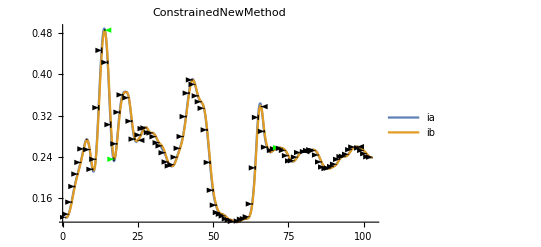

```mathematica
seeAllLine[n,u,listv0,condition,Range[1,103],pyrab[[1;;1]],e,"ConstrainedNewMethod"]
```